p290

Doing part a) manually. I need to expand
	...+(c_5 t^5)/(t+1)^5+(c_4 t^4)/(t+1)^4+(c_3 t^3)/(t+1)^3+(c_2 t^2)/(t+1)^2+(c_1 t)/(t+1)
Since (t+1)^-1=∑_(k=0)^∞ t^k if |t|<1 we also have 
	-(t+1)^-2=∑_(k=0)^∞ k t^(k-1)
	-(t+1)^-3=∑_(k=0)^∞ k (k-1)t^(k-2)
	…
when |t|<1.   So we can put the pieces together.

```mathematica
Series[(t+1)^-2,{t,0, 5}]
Series[(t+1)^-3,{t,0, 5}]
Series[(t+1)^-4,{t,0, 5}]
```

1-2 t+3 t^2-4 t^3+5 t^4-6 t^5+O[t]^6

1-3 t+6 t^2-10 t^3+15 t^4-21 t^5+O[t]^6

1-4 t+10 t^2-20 t^3+35 t^4-56 t^5+O[t]^6

```mathematica
TS[t/(1+t)]
```

(c_5 t^5)/(t+1)^5+(c_4 t^4)/(t+1)^4+(c_3 t^3)/(t+1)^3+(c_2 t^2)/(t+1)^2+(c_1 t)/(t+1)

```mathematica
(t c[1])/(1+t)+(t^2 c[2])/(1+t)^2+(t^3 c[3])/(1+t)^3+(t^4 c[4])/(1+t)^4+(t^5 c[5])/(1+t)^5+
```

```mathematica
TS[z_]:=Sum[ Subscript[c, i] z^i,{i, 1, 5}]
Series[TS[t/(1+t)],{t, 0, 5}]
```

c_1 t+(-c_1+c_2) t^2+(c_1-2 c_2+c_3) t^3+(-c_1+3 c_2-3 c_3+c_4) t^4+(c_1-4 c_2+6 c_3-4 c_4+c_5) t^5+O[t]^6

```mathematica
Series[ArcTan[z],{z,0, 7}]
```

z-z^3/3+z^5/5-z^7/7+O[z]^8

The big question is what does the mapping z->z+z^-1 do to ℂ.  It is pretty clear it has a problem at z=0.  In polar coordinates it is r ⅇ^ⅈθ->(r+1/r)ⅇ^(ⅈ θ) and we can see that i

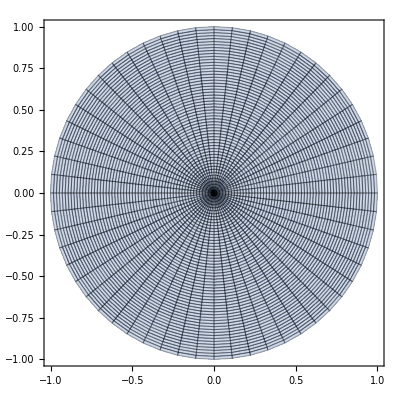

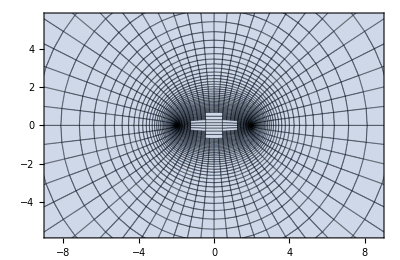

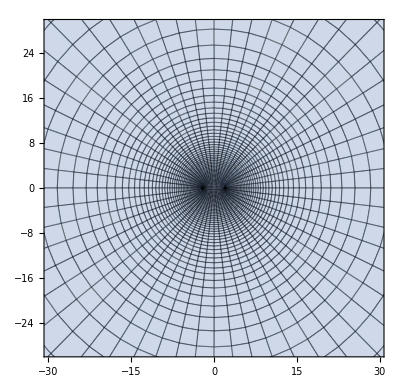

```mathematica
w[z_]:=z+1/z
ParametricPlot[ ReIm[r E^(ⅈ θ)],{r,0,1},{θ,0, 2π},
Mesh->All]
ParametricPlot[ ReIm[w[r E^(ⅈ θ)]],{r,0,1},{θ,0, 2π},
Mesh->All]
ParametricPlot[ ReIm[w[r E^(ⅈ θ)]],{r,1,∞},{θ,0, 2π},
Mesh->All]
```

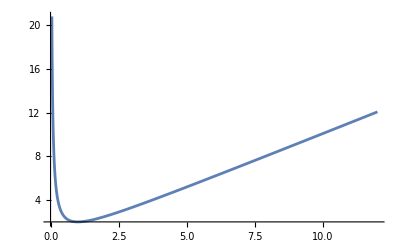

```mathematica
Plot[r+1/r,{r,0, 1}]
```

```mathematica
w[z_]:=Module[{s=√(z+1)√(z-1)},
1/π(s+Log[z+s])
]
TabView[{
"orig"->ParametricPlot[ReIm[x+ I y],{x, -10,4},{y,0,10},
PlotRange->All,Mesh->All],
"image"->ParametricPlot[ReIm[w[x+ I y]],{x, -10,4},{y,0,10},
PlotRange->All,Mesh->All]
},2]
```

12

p219

```mathematica
w[z_]:=Module[{s=√(z+1)√(z-1)},
2/π(s+ArcSin[1/z])
]
TabView[{
"orig"->ParametricPlot[ReIm[x+ I y],{x, -3,3},{y,0,2},
PlotRange->All,Mesh->All],
"image"->ParametricPlot[ReIm[w[x+ I y]],{x, -3,3},{y,0,2},
PlotRange->All,Mesh->All,
PlotPoints->100]
},2]
```

12

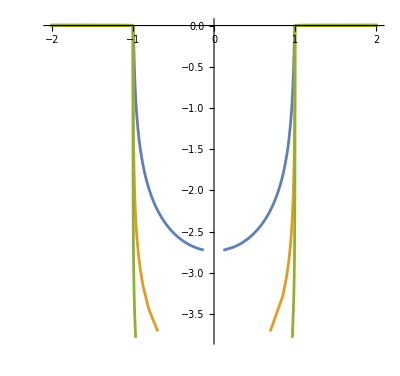

```mathematica
ϵ=10^-3;
ParametricPlot[Evaluate[Table[ReIm[w[x+ϵ I]],{ϵ,{0.01,0.001,0.0001}}]],{x,-3,3},PlotRange->All]
```

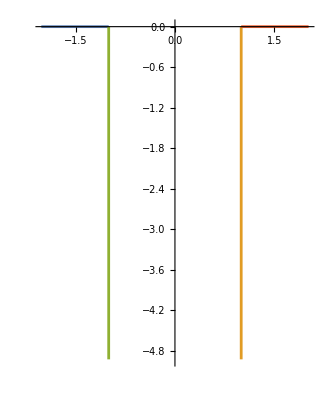

```mathematica
ParametricPlot[{
ReIm[w[-1-2x+10^-12 I]],
ReIm[w[x+10^-12 I]],
ReIm[w[-x+10^-12 I]],
ReIm[w[1+2x+10^-12 I]]
},{x,0,1},PlotRange->All]
```

p221

```mathematica
w[z_]:=0.5(z+1/z)
TabView[{
"orig"->ParametricPlot[ReIm[r E^(ⅈ θ)],{r, 1,6},{θ,0,π},
PlotRange->All,Mesh->All],
"image"->ParametricPlot[ReIm[w[r E^(ⅈ θ)]],{r, 1,6},{θ,0,π},
PlotRange->All,Mesh->All,
PlotPoints->20]
},2]
```

12

# Schwarz-Christoffel

If I have a bunch of points on the real axis 
	A_1<A_2<…<A_(n-1)<A_n=∞
and a bunch of positive exponents β_1,β_2,…,β_n satisfying 
	1<∑_(k=1)^n β_k
and define
	S[z]=∫_0^z 1/(∏_(k=1)^(n-1) (ζ-A_k)^β_k)dζ

Lets see what happens with A_(1:3)={0,1,∞} and β_(1:3)={0.5,0.5,0}

1/((-1.+ζ)^0.5 (0.+ζ)^0.5)

-2. Log[√(-1.+ζ)-1. √ζ]

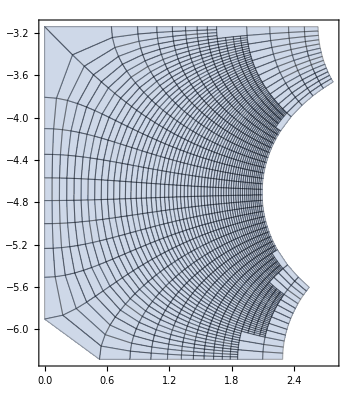

```mathematica
A={0.0,1.0,∞};
β={0.5,0.5,0};
n=Length[β];
SCIntegrand=Product[(ζ-A⟦i⟧)^(-β⟦i⟧),{i,1,n-1}]
SC[ζ_]=Integrate[SCIntegrand,ζ]

ParametricPlot[ReIm[SC[x+I y]],{x,-3,3},{y,0,2},
Mesh->All]
```